```mathematica
SetDirectory["\\\\cfs\\users\\wd26\\Documents\\Downloads"]
```

\\cfs\users\wd26\Documents\Downloads

```mathematica
<< KnotTheory`
```

ParentDirectory::nums: Argument File should be a positive machine-size integer, a nonempty string, or a File specification.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[{File,WikiLink,mathematica}].

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[{File,QuantumGroups}].

Loading KnotTheory` version of September 6, 2014, 13:37:37.2841.
Read more at http://katlas.org/wiki/KnotTheory.

```mathematica
sm = MorseLink[Cup[2,1],Cup[3,4],X[2,Over,Down,Down],X[3,Under,Down,Up],X[2,Under,Down,Up],X[1,Under,Up,Up],X[3,Over,Down,Down],X[1,Under,Up,Up],X[3,Over,Down,Down],Cap[2,3],Cap[1,2]];
```

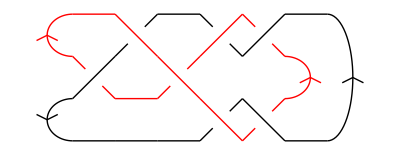

```mathematica
Show[DrawMorseLink[sm]]
```

```mathematica
ps = PD[sm]
js = Jones[ps][q]
```

```mathematica
bm = MorseLink[Cup[1,2],Cup[3,4],Cup[5,6],X[2,Under,Up,Down],X[4,Under,Up,Down],X[1,Over,Down,Down],Cap[3,4],X[3,Over,Up,Up],X[1,Under,Down,Down],Cup[4,3],X[1,Under,Down,Down],X[4,Under,Down,Up],X[2,Over,Down,Up],X[5,Under,Down,Up],X[3,Over,Down,Up],X[5,Over,Up,Down],X[2,Over,Up,Up],Cap[6,5],X[1,Over,Down,Up],Cap[3,2],Cap[1,2]];
```

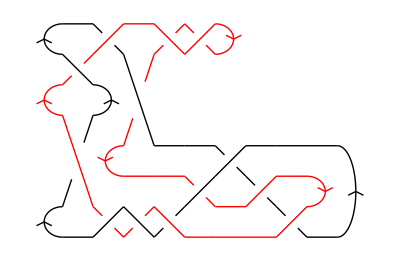

```mathematica
Show[DrawMorseLink[bm]]
```

```mathematica
pb = PD[bm];
```

```mathematica
jb = Jones[pb][q]
```

-√q-q^(5/2)

```mathematica
js==jb
```

True